```mathematica
actual[d_,r_,cat_,catAll_,debrisPerDeploy_,years_]:=(1-r)(debrisPerDeploy)((1-cat)((1-(1-cat)^(d*years))/cat))(1-catAll);
Manipulate[
run=maxD;
rise=actual[maxD,r,cat,catAll,debrisPerDeploy,years];
slope=rise/run;
plot=Plot[{
actual[d,r,cat,catAll,debrisPerDeploy,years],
slope*d
},
{d,0,maxD},
PlotTheme->"Monochrome",
AxesLabel->{"Dep_i","debris/(deployments/yr)"},
PlotLegends->{"DebrisActual","Approximation"}]
,
{r,0.001,1},
{cat,0.001,1},
{catAll,0.001,1},
{debrisPerDeploy,1,8},
{maxD,1,8,1},
{years,1,20,1}
]
```

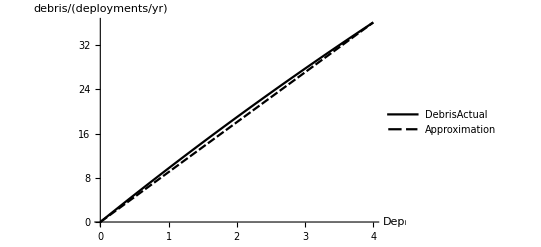

```mathematica
plot
```